## Appendix A1 (Linear stability analysis of two-species interaction)

### → Species only differ in soil and resource preference; Intrinsic growth rate is quadratic

```mathematica
ClearAll["α","β"]
```

#### Eq(1) from the paper. Using S instead of E since mathematica does not allow that.

```mathematica
Subscript[dN, 1]=Subscript[N, 1](1-S^2/ω^2-(β Subscript[N, 1]+α Subscript[N, 2]));
Subscript[dN, 2]=Subscript[N, 2](1-(S-ϵ)^2/ω^2-(α Subscript[N, 1]+β Subscript[N, 2]));
dS=(-S)Subscript[N, 1]+(ϵ-S)Subscript[N, 2];
```

#### Equilibrium

```mathematica
eqN=FullSimplify[Solve[Subscript[dN, 1]==0&&Subscript[dN, 2]==0,{Subscript[N, 1],Subscript[N, 2]}]]
```

{{N_1→0,N_2→0},{N_1→0,N_2→(-(S-ϵ)^2+ω^2)/(β ω^2)},{N_1→(1+(S^2 (-α+β)+2 S α ϵ-α ϵ^2)/((α-β) ω^2))/(α+β),N_2→(1+(S^2 (-α+β)-2 S β ϵ+β ϵ^2)/((α-β) ω^2))/(α+β)},{N_1→(1-S^2/ω^2)/β,N_2→0}}

→ Four equilibrium. (1) Both extinct, (2) Only species 1 persists, (3) Coexistence, (4) Only species 2 persists

```mathematica
eqS1=FullSimplify[Solve[(dS/.eqN[[3]])==0,S]]
```

{{S→ϵ/2},{S→1/2 (ϵ-(√((α+3 β) ϵ^2+4 (α-β) ω^2))/(√(α-β)))},{S→1/2 (ϵ+(√((α+3 β) ϵ^2+4 (α-β) ω^2))/(√(α-β)))}}

```mathematica
FullSimplify[Reduce[(α+3 β) ϵ^2+4 (α-β) ω^2>0&&α>0&&β>0&&ω>0&&ϵ>0,ϵ]]
```

β>0&&ω>0&&((ϵ>2 √((-α+β)/(α+3 β)) ω&&0<α<β)||(ϵ>0&&α≥β))

→ All three roots are real when α≥β or ϵ is sufficiently large. Let [C1] be ϵ>2 √((-α+β)/(α+3 β)) ω && 0<α<β.

```mathematica
FullSimplify[eqN[[3]]/.eqS1[[1]]]
```

{N_1→(4-ϵ^2/ω^2)/(4 (α+β)),N_2→(4-ϵ^2/ω^2)/(4 (α+β))}

→ Symmetric equilibria are feasible only when  -2ω < ϵ < 2ω or ϵ^2<4 ω^2 .

#### Stability

```mathematica
Jc={{D[Subscript[dN, 1],Subscript[N, 1]],D[Subscript[dN, 1],Subscript[N, 2]],D[Subscript[dN, 1],S]},{D[Subscript[dN, 2],Subscript[N, 1]],D[Subscript[dN, 2],Subscript[N, 2]],D[Subscript[dN, 2],S]},{D[dS,Subscript[N, 1]],D[dS,Subscript[N, 2]],D[dS,S]}}
```

{{1-S^2/ω^2-2 β N_1-α N_2,-α N_1,-(2 S N_1)/ω^2},{-α N_2,1-(S-ϵ)^2/ω^2-α N_1-2 β N_2,-(2 (S-ϵ) N_2)/ω^2},{-S,-S+ϵ,-N_1-N_2}}

```mathematica
FullSimplify[Eigensystem[Jc/.eqN[[1]]]]
```

{{0,1-S^2/ω^2,1-(S-ϵ)^2/ω^2},{{0,0,1},{-1/S+S/ω^2,0,1},{0,1/(-S+ϵ)+(S-ϵ)/ω^2,1}}}

→ Extinction is never stable. It is stable on the N_1 x N_2 plane when S is not within the fundamental niche of either species.

```mathematica
FullSimplify[Eigenvalues[Jc/.eqN[[2]]/.S-> ϵ]]
```

{-1/β,-1,1-α/β-ϵ^2/ω^2}

→ Competitive exclusion is stable when ϵ^2 > ω^2(1-α/β) .

```mathematica
FullSimplify[Eigenvalues[Jc/.eqN[[3]]/.eqS1[[1]]]]
```

{-1+ϵ^2/(4 ω^2),((2-α+β) ϵ^2 ω^2+4 (-2+α-β) ω^4-√(ω^4 (-ϵ^2+4 ω^2) (-((4+α^2+(-20+β) β-2 α (6+β)) ϵ^2)+4 (2+α-β)^2 ω^2)))/(8 (α+β) ω^4),((2-α+β) ϵ^2 ω^2+4 (-2+α-β) ω^4+√(ω^4 (-ϵ^2+4 ω^2) (-((4+α^2+(-20+β) β-2 α (6+β)) ϵ^2)+4 (2+α-β)^2 ω^2)))/(8 (α+β) ω^4)}

```mathematica
FullSimplify[Reduce[ω^4 (-ϵ^2+4 ω^2) (-((4+α^2+(-20+β) β-2 α (6+β)) ϵ^2)+4 (2+α-β)^2 ω^2)>0&&ω>0&&α>0&&β>0&&0<ϵ<2ω,ϵ]]
```

β>0&&α>0&&0<ϵ<2 ω

→  The eigenvalues are real whenever the symmetric coexistence equilibria are feasible

```mathematica
FullSimplify[Reduce[(2-α+β) ϵ^2 ω^2+4 (-2+α-β) ω^4+√(ω^4 (-ϵ^2+4 ω^2) (-((4+α^2+(-20+β) β-2 α (6+β)) ϵ^2)+4 (2+α-β)^2 ω^2))<0&&ω>0&&α>0&&β>0&&α-β<2&&0<ϵ<2ω,ϵ]]
```

0<α<β&&ω>0&&0<ϵ<2 √((-α+β)/(α+3 β)) ω

→  Asymmetric equilibrium is never stable because at the stability condition, the equilibria (S value) is not feasible [C1].

#### Competition coefficient (α) calculation

```mathematica
ClearAll["αc","βc","f"]
```

```mathematica
f[ν_,σ_,ζ_]:=ν NIntegrate[Exp[-x^2/σ^2]Exp[(-(x-ζ)^4)/(81 σ^4)],{x,-Infinity,Infinity}]/NIntegrate[Exp[-x^2/σ^2]^2,{x,-Infinity,Infinity}]
```

#### Figure 2a equivalent for quadratic intrinsic growth rate

```mathematica
par={ω->1,σ->1,ν->1};
```

```mathematica
αc=f[ν,σ,ζ]/.par;
```

NIntegrate::inumr: The integrand ⅇ^(-(x-ζ)^4/(81 σ^4)-x^2/σ^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

NIntegrate::inumr: The integrand ⅇ^(-(2 x^2)/σ^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate::inumr: The integrand ⅇ^(-x^2-1/81 (x-ζ)^4) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
βc=f[ν,σ,0]/.par;
```

NIntegrate::inumr: The integrand ⅇ^(-x^4/(81 σ^4)-x^2/σ^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate::inumr: The integrand ⅇ^(-(2 x^2)/σ^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

→  The warnings are present because ζ is unspecified.

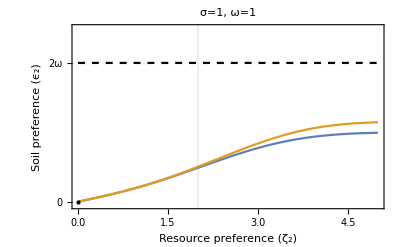

```mathematica
figA1=Plot[{(ω√(1-αc/βc))/.par,(2 ω√((1-αc/βc)/(3+αc/βc)))/.par,2ω/.par},{ζ,0,5},PlotRange->{Automatic,{-0.05,2.5ω/.par}},PlotStyle->{{ColorData[97,1]},{ColorData[97,2]},{Black,Dashed}},Frame-> True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},PlotLabel->"σ=1, ω=1",LabelStyle->{FontSize->20,FontColor->Black},FrameTicks->{{{0,{2(ω/.par),"2ω"}},{{(ω/.par),"ω"},{N[2(ω/.par)/√3],"2ω/√3"}}},{Automatic,Automatic}},FrameTicksStyle->9,GridLines->{{2},{}},Epilog-> {PointSize[Large],Point[{0,0}]}]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA1.pdf", figS1];
```